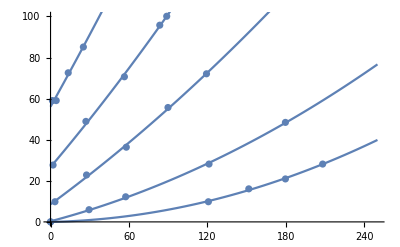

```mathematica
(*Рис.3а*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\1а.png"];
i = 5;
j = 5;
NewArr = Array[f, {i, j}];
data1a5 = {{0, 0}, {208.09898989898983, 28.155555555555537}, {179.61212121212117, 20.913131313131288}, {151.60808080808079, 16.084848484848465}, {120.70707070707068, 9.808080808080788}, {91.73737373737372, 6.911111111111097}, {56.49090909090907, 3.5313131313131123}, {28.96969696969696, 1.59999999999998}};
data1a6 = {{0, 0}, {179.61212121212117, 48.43434343434343}, {121.18989898989896, 28.15555555555555}, {57.456565656565644, 12.222222222222214}, {29.45252525252525, 5.945454545454538}};
data1a7 = {{3.379797979797978, 9.808080808080803}, {119.25858585858582, 72.0929292929293}, {89.80606060606058, 55.67676767676768}, {57.93939393939392, 36.36363636363636}, {27.521212121212116, 22.84444444444445}};
data1a8 = {{1.9313131313131322, 27.672727272727272}, {88.84040404040402, 100.0969696969697}, {56.49090909090907, 70.64444444444445}, {27.03838383838383, 48.917171717171726}, {83.52929292929291, 95.75151515151515}};
data1a9 = {{4.345454545454544, 59.05656565656565}, {40.55757575757575, 103.95959595959596}, {25.107070707070697, 85.12929292929293}, {13.519191919191918, 72.57575757575758}, {1.4484848484848456, 59.05656565656565}};
For [k = 0, k < j,  NewArr[[1]][[k]] = data1a5[[k]], k++];
For [k = 0, k < j,  NewArr[[2]][[k]] = data1a6[[k]], k++];
For [k = 0, k < j,  NewArr[[3]][[k]] = data1a7[[k]], k++];
For [k = 0, k < j,  NewArr[[4]][[k]] = data1a8[[k]], k++];
For [k = 0, k < j,  NewArr[[5]][[k]] = data1a9[[k]], k++];
fun[x_] = Fit[NewArr[[1]], {1, x, x*x}, x];
g11 = Show[ListPlot[NewArr[[1]]], Plot[fun[x], {x, 0, 250}], PlotRange -> {{0, 250}, {0, 100}}];
fun[x_] = Fit[NewArr[[2]], {1, x, x*x}, x];
g12 = Show[ListPlot[NewArr[[2]]], Plot[fun[x], {x, 0, 250}], PlotRange -> {{0, 250}, {0, 100}}];
fun[x_] = Fit[NewArr[[3]], {1, x, x*x}, x];
g13 = Show[ListPlot[NewArr[[3]]], Plot[fun[x], {x, 0, 250}], PlotRange -> {{0, 150}, {0, 60}}];
fun[x_] = Fit[NewArr[[4]], {1, x, x*x}, x];
g14 = Show[ListPlot[NewArr[[4]]], Plot[fun[x], {x, 0, 250}], PlotRange -> {{0, 250}, {0, 100}}];
fun[x_] = Fit[NewArr[[5]], {1, x, x*x}, x];
g15 = Show[ListPlot[NewArr[[5]]], Plot[fun[x], {x, 0, 250}], PlotRange -> {{0, 250}, {0, 100}}];
Show[g11, g12, g13, g14, g15]
```

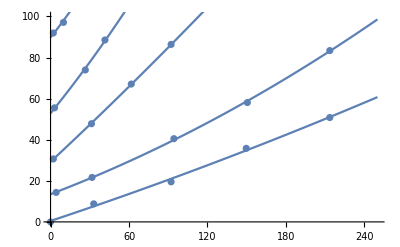

```mathematica
(*Рис.3б*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\1б.png"];
data1a5={{0,0},{213.5536028119508,50.80140597539544},{149.65905096660808,35.792618629174},{92.19683655536029,19.49736379613357},{33.019332161687174,8.776801405975391}};
data1a6 = {{213.5536028119508,83.39191564147629},{150.51669595782076,58.091388400702996},{94.34094903339192,40.50966608084359},{31.732864674868196,21.641476274165214},{4.288224956063274,14.351493848857658}};
data1a7= {{120.07029876977154,104.4042179261863},{92.19683655536029,86.39367311072057},{61.750439367311074,67.09666080843586},{31.304042179261863,47.799648506151144},{2.144112478031637,30.646748681898075}};
data1a8 = {{83.62038664323374,128.84710017574693},{63.03690685413005,108.69244288224957},{41.59578207381371,88.5377855887522},{26.58699472759227,73.95782073813709},{3.001757469244289,55.51845342706504}};
data1a9 = {{39.880492091388405,126.7029876977153},{28.731107205623907,115.98242530755712},{19.297012302284713,106.54833040421794},{9.86291739894552,97.11423550087875},{2.144112478031637,91.96836555360282}};
For [k=0, k<j,  NewArr[[1]][[k]]=data1a5[[k]], k++];
For [k=0, k<j,  NewArr[[2]][[k]]=data1a6[[k]], k++];
For [k=0, k<j,  NewArr[[3]][[k]]=data1a7[[k]], k++];
For [k=0, k<j,  NewArr[[4]][[k]]=data1a8[[k]], k++];
For [k=0, k<j,  NewArr[[5]][[k]]=data1a9[[k]], k++];
fun[x_]=Fit[NewArr[[1]],{1,x,x*x},x];
g11 =Show[ListPlot[NewArr[[1]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr[[2]],{1,x,x*x},x];
g12 =Show[ListPlot[NewArr[[2]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr[[3]],{1,x,x*x},x];
g13 =Show[ListPlot[NewArr[[3]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,150},{0,60}}];
fun[x_]=Fit[NewArr[[4]],{1,x,x*x},x];
g14 =Show[ListPlot[NewArr[[4]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr[[5]],{1,x,x*x},x];
g15 =Show[ListPlot[NewArr[[5]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
Show[g11,g12,g13,g14,g15]
```

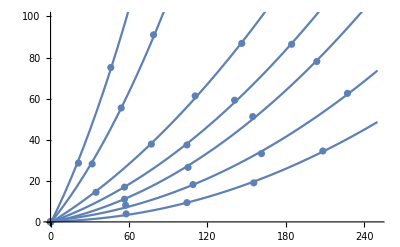

```mathematica
(*Рис.4а*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\4а.png"];
i=7;
j=5;
NewArr1 = Array[f, {i,j}];
data4a1={{0,0},{208.23567921440264,34.50736497545006},{155.44353518821603,19.004909983633354},{104.32733224222585,9.368248772504074},{57.81996726677578,3.9214402618657687}};
data4a2 = {{0,0},{227.09001636661213,62.57937806873976},{161.30932896890343,33.25040916530276},{108.93617021276597,18.16693944353517},{57.400981996726685,8.11129296235677}};
data4a3= {{0,0},{203.62684124386251,78.08183306055645},{154.60556464811785,51.266775777414054},{105.16530278232406,26.546644844517168},{56.56301145662847,11.04418985270047}};
data4a4 = {{0,0},{184.35351882160393,86.46153846153844},{140.77905073649754,59.22749590834695},{104.32733224222585,37.44026186579376},{56.56301145662847,16.909983633387867}};
data4a5= {{0,0},{146.22585924713584,86.88052373158754},{110.61211129296237,61.322422258592454},{77.09328968903438,37.859247135842864},{34.77577741407529,14.396072013093274}};
data4a6= {{0,0},{106.84124386252046,135.90180032733218},{78.76923076923077,91.07037643207852},{54.04909983633388,55.45662847790503},{31.84288052373159,28.22258592471354}};
data4a7= {{0,0},{84.21603927986907,161.04091653027822},{64.10474631751228,113.27659574468083},{46.08837970540098,75.14893617021275},{21.368248772504092,28.641571194762662}};
For [k=0, k<j,  NewArr1[[1]][[k]]=data4a1[[k]], k++];
For [k=0, k<j,  NewArr1[[2]][[k]]=data4a2[[k]], k++];
For [k=0, k<j,  NewArr1[[3]][[k]]=data4a3[[k]], k++];
For [k=0, k<j,  NewArr1[[4]][[k]]=data4a4[[k]], k++];
For [k=0, k<j,  NewArr1[[5]][[k]]=data4a5[[k]], k++];
For [k=0, k<j,  NewArr1[[6]][[k]]=data4a6[[k]], k++];
For [k=0, k<j,  NewArr1[[7]][[k]]=data4a7[[k]], k++];
fun[x_]=Fit[NewArr1[[1]],{1,x,x*x},x];
g11 =Show[ListPlot[NewArr1[[1]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[2]],{1,x,x*x},x];
g12 =Show[ListPlot[NewArr1[[2]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[3]],{1,x,x*x},x];
g13 =Show[ListPlot[NewArr1[[3]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,150},{0,60}}];
fun[x_]=Fit[NewArr1[[4]],{1,x,x*x},x];
g14 =Show[ListPlot[NewArr1[[4]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[5]],{1,x,x*x},x];
g15 =Show[ListPlot[NewArr1[[5]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[6]],{1,x,x*x},x];
g16 =Show[ListPlot[NewArr1[[6]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[7]],{1,x,x*x},x];
g17 =Show[ListPlot[NewArr1[[7]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
Show[g11,g12,g13,g14,g15, g16, g17]
```

```mathematica
(*Рис.4б*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\4б.png"];
i=7;
j=5;
NewArr1 = Array[f, {i,j}];
data4a1={{0,0},{182.65051020408163,65.28571428571428},{155.54336734693877,47.859693877551024},{118.10969387755102,27.852040816326536},{80.67602040816328,13.65306122448979}};
data4a2 = {{0,0},{176.19642857142858,100.78316326530613},{138.7627551020408,67.22193877551021},{91.64795918367346,34.95153061224491},{54.85969387755103,15.589285714285722}};
data4a3= {{0,0},{168.4515306122449,140.79846938775512},{123.27295918367346,86.5841836734694},{87.77551020408163,51.08673469387756},{56.150510204081634,25.91581632653063}};
data4a4 = {{0,0},{152.31632653061226,173.0688775510204},{118.75510204081633,121.43622448979592},{87.13010204081633,77.54846938775509},{56.79591836734695,42.696428571428584}};
data4a5= {{0,0},{127.7908163265306,180.8137755102041},{95.5204081632653,123.37244897959185},{70.99489795918367,82.71173469387756},{45.17857142857144,47.85969387755105}};
data4a6= {{0,0},{70.34948979591837,175.6505102040816},{53.568877551020414,120.79081632653057},{36.142857142857146,73.67602040816325},{20.653061224489797,34.95153061224488}};
data4a7= {{0,0},{53.568877551020414,212.43877551020404},{40.660714285714285,149.83418367346937},{29.68877551020409,102.07397959183672},{14.19897959183674,49.15051020408163}};
For [k=0, k<j,  NewArr1[[1]][[k]]=data4a1[[k]], k++];
For [k=0, k<j,  NewArr1[[2]][[k]]=data4a2[[k]], k++];
For [k=0, k<j,  NewArr1[[3]][[k]]=data4a3[[k]], k++];
For [k=0, k<j,  NewArr1[[4]][[k]]=data4a4[[k]], k++];
For [k=0, k<j,  NewArr1[[5]][[k]]=data4a5[[k]], k++];
For [k=0, k<j,  NewArr1[[6]][[k]]=data4a6[[k]], k++];
For [k=0, k<j,  NewArr1[[7]][[k]]=data4a7[[k]], k++];
fun[x_]=Fit[NewArr1[[1]],{1,x,x*x},x];
g11 =Show[ListPlot[NewArr1[[1]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[2]],{1,x,x*x},x];
g12 =Show[ListPlot[NewArr1[[2]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[3]],{1,x,x*x},x];
g13 =Show[ListPlot[NewArr1[[3]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,150},{0,60}}];
fun[x_]=Fit[NewArr1[[4]],{1,x,x*x},x];
g14 =Show[ListPlot[NewArr1[[4]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[5]],{1,x,x*x},x];
g15 =Show[ListPlot[NewArr1[[5]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[6]],{1,x,x*x},x];
g16 =Show[ListPlot[NewArr1[[6]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[7]],{1,x,x*x},x];
g17 =Show[ListPlot[NewArr1[[7]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
Show[g11,g12,g13,g14,g15, g16, g17]
```

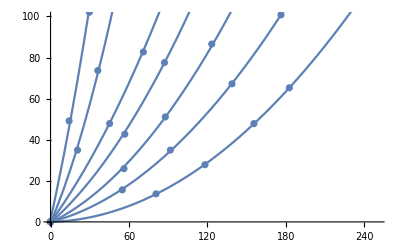

```mathematica
(*Рис.4с*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\4б.png"];
i=7;
j=5;
NewArr1 = Array[f, {i,j}];
data4a1={{0,0},{196.82204724409442,58.442519685039386},{158.57322834645666,37.325984251968535},{134.66771653543304,25.373228346456713},{99.60629921259839,12.623622047244112}};
data4a2 = {{0,0},{181.28346456692907,81.94960629921262},{146.22204724409445,57.645669291338606},{123.511811023622,41.70866141732286},{75.30236220472437,18.600000000000037}};
data4a3= {{0,0},{155.3858267716535,103.06614173228348},{117.9338582677165,65.21574803149609},{88.45039370078736,41.70866141732286},{52.99055118110233,19.396850393700817}};
data4a4 = {{0,0},{154.1905511811023,136.93228346456695},{117.13700787401571,95.09763779527562},{85.26299212598421,64.02047244094491},{51.79527559055116,34.93543307086617}};
data4a5= {{0,0},{130.2850393700787,148.08818897637798},{103.98897637795271,111.03464566929136},{78.88818897637792,79.16062992125987},{50.20157480314958,50.075590551181136}};
data4a6= {{0,0},{80.88031496062989,194.30551181102362},{60.56062992125982,130.55748031496063},{46.61574803149604,96.69133858267719},{25.897637795275582,50.872440944881916}};
data4a7= {{0,0},{56.974803149606274,191.91496062992127},{43.42834645669289,138.9244094488189},{31.47559055118109,91.91023622047246},{17.929133858267708,52.8645669291339}};
For [k=0, k<j,  NewArr1[[1]][[k]]=data4a1[[k]], k++];
For [k=0, k<j,  NewArr1[[2]][[k]]=data4a2[[k]], k++];
For [k=0, k<j,  NewArr1[[3]][[k]]=data4a3[[k]], k++];
For [k=0, k<j,  NewArr1[[4]][[k]]=data4a4[[k]], k++];
For [k=0, k<j,  NewArr1[[5]][[k]]=data4a5[[k]], k++];
For [k=0, k<j,  NewArr1[[6]][[k]]=data4a6[[k]], k++];
For [k=0, k<j,  NewArr1[[7]][[k]]=data4a7[[k]], k++];
fun[x_]=Fit[NewArr1[[1]],{1,x,x*x},x];
g11 =Show[ListPlot[NewArr1[[1]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[2]],{1,x,x*x},x];
g12 =Show[ListPlot[NewArr1[[2]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[3]],{1,x,x*x},x];
g13 =Show[ListPlot[NewArr1[[3]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,150},{0,60}}];
fun[x_]=Fit[NewArr1[[4]],{1,x,x*x},x];
g14 =Show[ListPlot[NewArr1[[4]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[5]],{1,x,x*x},x];
g15 =Show[ListPlot[NewArr1[[5]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[6]],{1,x,x*x},x];
g16 =Show[ListPlot[NewArr1[[6]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[7]],{1,x,x*x},x];
g17 =Show[ListPlot[NewArr1[[7]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
Show[g11,g12,g13,g14,g15, g16, g17]
```

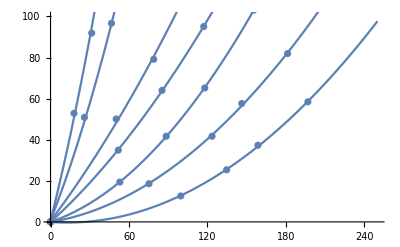

```mathematica
(*Рис.4д*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\4б.png"];
i=7;
j=5;
NewArr1 = Array[f, {i,j}];
data4a1={{0,0},{239.51150442477876,49.283185840707986},{177.96106194690265,26.090265486725684},{128.45309734513273,13.155752212389416},{80.729203539823,5.573451327433645}};
data4a2 = {{0,0},{222.5628318584071,63.55575221238939},{169.04070796460178,38.132743362831874},{128.0070796460177,24.3061946902655},{78.05309734513274,11.817699115044263}};
data4a3= {{0,0},{231.929203539823,105.92743362831861},{180.6371681415929,69.80000000000003},{140.0495575221239,47.4991150442478},{77.16106194690265,21.18407079646019}};
data4a4 = {{0,0},{233.26725663716815,134.91858407079647},{177.96106194690265,91.20884955752214},{126.22300884955753,55.97345132743365},{76.7150442477876,29.658407079646025}};
data4a5= {{0,0},{206.95221238938052,153.2053097345133},{164.13451327433626,110.38761061946904},{119.53274336283185,72.47610619469029},{73.14690265486726,39.02477876106197}};
data4a6= {{0,0},{111.50442477876105,153.20530973451332},{110.61238938053098,153.20530973451332},{86.97345132743362,106.37345132743367},{64.67256637168141,70.6920353982301}};
data4a7= {{0,0},{95.89380530973452,204.0513274336283},{74.03893805309734,145.17699115044246},{51.292035398230084,91.20884955752217},{29.43716814159292,46.60707964601772}};
For [k=0, k<j,  NewArr1[[1]][[k]]=data4a1[[k]], k++];
For [k=0, k<j,  NewArr1[[2]][[k]]=data4a2[[k]], k++];
For [k=0, k<j,  NewArr1[[3]][[k]]=data4a3[[k]], k++];
For [k=0, k<j,  NewArr1[[4]][[k]]=data4a4[[k]], k++];
For [k=0, k<j,  NewArr1[[5]][[k]]=data4a5[[k]], k++];
For [k=0, k<j,  NewArr1[[6]][[k]]=data4a6[[k]], k++];
For [k=0, k<j,  NewArr1[[7]][[k]]=data4a7[[k]], k++];
fun[x_]=Fit[NewArr1[[1]],{1,x,x*x},x];
g11 =Show[ListPlot[NewArr1[[1]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[2]],{1,x,x*x},x];
g12 =Show[ListPlot[NewArr1[[2]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[3]],{1,x,x*x},x];
g13 =Show[ListPlot[NewArr1[[3]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,150},{0,60}}];
fun[x_]=Fit[NewArr1[[4]],{1,x,x*x},x];
g14 =Show[ListPlot[NewArr1[[4]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[5]],{1,x,x*x},x];
g15 =Show[ListPlot[NewArr1[[5]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[6]],{1,x,x*x},x];
g16 =Show[ListPlot[NewArr1[[6]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
fun[x_]=Fit[NewArr1[[7]],{1,x,x*x},x];
g17 =Show[ListPlot[NewArr1[[7]]],Plot[fun[x],{x,0,250}], PlotRange->{{0,250},{0,100}}];
Show[g11,g12,g13,g14,g15, g16, g17]
```

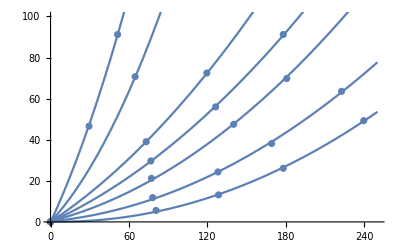

```mathematica
(*Рис.5*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\5.png"];
data51={{363.,502.},{320.,415.},{260.,304.},{169.,172.},{79.,60.}};
data52 = {{481.,425.},{374.,345.},{260.,253.},{169.,172.},{76.,82.}};
fun[x_]=Fit[data51,{1,x,x*x},x];
g11 =Show[ListPlot[data51],Plot[fun[x],{x,0,500}], PlotRange->{{0,500},{0,500}}];
fun[x_]=Fit[data52,{1,x,x*x},x];
g12 =Show[ListPlot[data52],Plot[fun[x],{x,0,500}], PlotRange->{{0,500},{0,500}}];
Show[g11,g12]
```

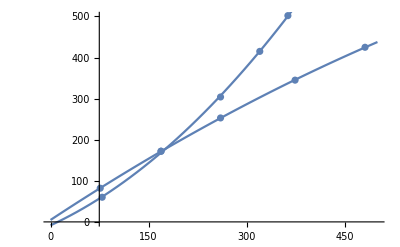

```mathematica
(*Рис.6*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\6.png"];
data61 = {{408.,115.},{288.,177.},{202.,238.},{115.,310.},{49.,384.}};
data62 = {{573.3568521031208,93.36092265943017},{517.5576662143826,101.44776119402991},{481.9755766621438,106.29986431478972},{447.20217096336495,109.53459972862964},{408.,115.}};
fun[x_]=Fit[data61,{1,x,x*x},x];
g11 =Show[ListPlot[data61],Plot[fun[x],{x,0,408}], PlotRange->{{0,600},{0,500}}];
fun[x_]=Fit[data62,{1,x,x*x},x];
g12 =Show[ListPlot[data62],Plot[fun[x],{x,409,600},PlotStyle->Dotted], PlotRange->{{0,600},{0,500}}];
Show[g11,g12]
```

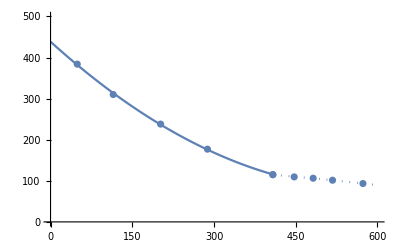

```mathematica
(*Рис.7*)
Import["C:\\Users\\variable\\Desktop\\Интерполяция\7.png"];
data71 = {{503.,452.},{430.,397.},{346.,318.},{276.,235.},{211.,147.},{150.,43.}};
data72 = {{503.,452.},{541.,454.}};
fun[x_]=Fit[data71,{1,x,x*x},x];
g11 =Show[ListPlot[data71],Plot[fun[x],{x,0,503}], PlotRange->{{0,600},{0,500}}];
fun[x_]=Fit[data72,{1,x,x*x},x];
g12 =Show[ListPlot[data72],Plot[fun[x],{x,503,542}], PlotRange->{{0,600},{0,500}}];
Show[g11,g12]
```